8.64×10^-6

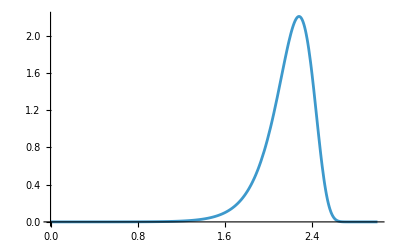

```mathematica
factor = 10^4*10^3*10^-23*10^6*3600*24.
σ = 1.;
Subscript[λ, A] = 6.;
Subscript[λ, B] = 2.;
β = 2.5;
Plot[Table[factor*(10^(-0.1*k))^σ*Exp[Subscript[λ, A]*t]*Exp[-(factor*(10^(-0.1*k))^σ)/Subscript[λ, A]*(Exp[Subscript[λ, A]*t]-1) ], {k,1, 1 }], {t, 0, 3.}, PlotRange->Full]
```

```mathematica
ζ =(Subscript[λ, B]/Subscript[λ, A]+1)/β
Subscript[ζ, 2] = ζ*(1/σ+ 1+ Subscript[λ, B]/Subscript[λ, A])
```

0.533333

1.24444

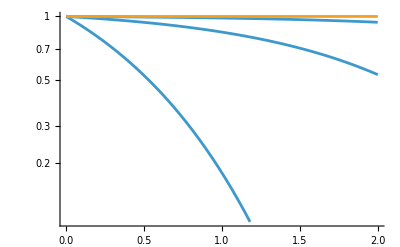

```mathematica
LogPlot[{Table[(Exp[-10^k*(Exp[t]-1)/10^2]), {k, 0, 2}], 1}, {t,0, 2}]
```

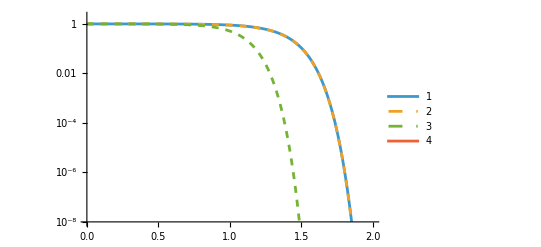

```mathematica
γ = .01;
LogPlot[{
Exp[-(1/Subscript[λ, A](Exp[Subscript[λ, A]*t]-1)-1/(Subscript[λ, A]+γ)(Exp[Subscript[λ, A]*t] - Exp[-γ *t]))],
Exp[-((ⅇ^(Subscript[λ, A] t)+Subscript[λ, A] t-1) γ)/Subscript[λ, A]^2],
Exp[-(γ*t)/Subscript[λ, A](Exp[Subscript[λ, A]*t]-1)],
(*Exp[-1/Subscript[λ, A](Exp[Subscript[λ, A]*t]-1)]*)
}, {t, 0, 2}, PlotRange->{Automatic, {10^-8, 2}}, PlotStyle->{ Solid,Dashed, Dashed}, PlotLegends->Automatic]
```

```mathematica
expr = FullSimplify[Exp[-(1/x(Exp[x*t]-1)-1/(x+y)(Exp[x*t] - Exp[-y *t]))]]
```

ⅇ^((x-ⅇ^(-t y) x+y-ⅇ^(t x) y)/(x^2+x y))

```mathematica
Normal@Series[expr/. y->ε x,{ε,0,1}]/. ε->y/x//FullSimplify
```

1+((1-ⅇ^(t x)+t x) y)/x^2

```mathematica
expexpr = -Log[expr]//FullSimplify
```

-Log[ⅇ^((x-ⅇ^(-t y) x+y-ⅇ^(t x) y)/(x^2+x y))]

```mathematica
Normal@Series[expexpr/. y->ε x,{ε,0,1}]/. ε->y/x//FullSimplify
```

((-1+ⅇ^(t x)-t x) y)/x^2